```mathematica
Clear["Global`*"]
```

```mathematica
$Assumptions = {T>0,L>0,ρ>0,2T>Δt>0,T>Δr>0};
```

```mathematica
Ci odd [d_,i_]:=Sum[Binomial[i-1,k](-1)^k Gamma[d/2(k+1)+3/2]/(Gamma[(d+3)/2]Gamma[1+(d k)/2]),{k,0,i-1}]
Ci even [d_,i_]:=Sum[Binomial[i-1,k](-1)^k Gamma[d/2(k+1)+2]/(Gamma[d/2+2]Gamma[1+(d k)/2]),{k,0,i-1}]
c[d_]:= (2^(1/2+(1-d)/2) π^(1/2 (-1+d)))/(d Gamma[1+1/2 (-1+d)])
α odd[d_]:= (-c[d]^(2/d))/Gamma[(d+2)/d]
α even[d_]:= (-2 c[d]^(2/d))/Gamma[(d+2)/d]
β odd[d_]:= (d+1)/(2^(d-1)Gamma[2/d+1])c[d]^(2/d)
β even[d_]:= (2Gamma[d/2+2]Gamma[d/2+1])/(Gamma[2/d]Gamma[d])c[d]^(2/d)
O d odd[I1_,d_]:=Sum[Abs[Ci odd [d,i]] 1/((i-1)!)ρ^(i-1)D[I1,{ρ,i-1}],{i,1,(d+3)/2}]
O d even[I1_,d_]:=Sum[Abs[Ci even[d,i]] 1/((i-1)!)ρ^(i-1)D[I1,{ρ,i-1}],{i,1,(d+4)/2}]
Integrand[d_] := (4 π^(-1+d/2) Δr^(-2+d) (T-Δt) (-Δr/(-2+d)+(L √π Gamma[-1+d/2])/(2 Gamma[1/2 (-1+d)])))/Gamma[-1+d/2] Exp[-ρ (2^(1-d) π^(1/2 (-1+d)) ((-Δr+Δt) (Δr+Δt))^(d/2))/(d Gamma[(1+d)/2])]/.L->1/.T->1
Even integrand[d_] := ρ^(1+2/d) O d even[Integrand[d],d]

Odd integrand[d_] :=ρ^(1+2/d) O d odd[Integrand[d],d]
```

```mathematica
(ρ^(1+2/d) O d even[(1-Δr)(1-Δt)Exp[-ρ (2^(1-d) π^(1/2 (-1+d)) ((-Δr+Δt) (Δr+Δt))^(d/2))/(d Gamma[(1+d)/2])],d]/.{d->2})//FullSimplify
```

1/8 ⅇ^(1/2 (Δr-Δt) (Δr+Δt) ρ) (-1+Δr) (-1+Δt) ρ^2 (8+(Δr-Δt) (Δr+Δt) ρ (8+(Δr-Δt) (Δr+Δt) ρ))

```mathematica
Odd integrand[3]//FullSimplify
```

1/64 ⅇ^(-1/12 π (-Δr^2+Δt^2)^(3/2) ρ) (π-2 Δr) Δr (-1+Δt) ρ^(5/3) (-128+36 π (-Δr^2+Δt^2)^(3/2) ρ+π^2 (Δr^2-Δt^2)^3 ρ^2)

```mathematica
Even integrand[4]//FullSimplify
```

-(ⅇ^(-1/24 π (Δr^2-Δt^2)^2 ρ) π (-2+Δr) Δr^2 (-1+Δt) ρ^(3/2) (-10368+π (Δr-Δt)^2 (Δr+Δt)^2 ρ (3888+π (Δr^2-Δt^2)^2 ρ (-144+π (Δr^2-Δt^2)^2 ρ))))/5184

```mathematica
i1[Δt_?NumericQ,ρ_?NumericQ]:=i1[Δt,ρ]=NIntegrate[-(ⅇ^(-1/24 π (Δr^2-Δt^2)^2 ρ) π (-2+Δr) Δr^2 (-1+Δt) ρ^(3/2) (-10368+π (Δr-Δt)^2 (Δr+Δt)^2 ρ (3888+π (Δr^2-Δt^2)^2 ρ (-144+π (Δr^2-Δt^2)^2 ρ))))/5184,{Δr,0,2-Δt}]
```

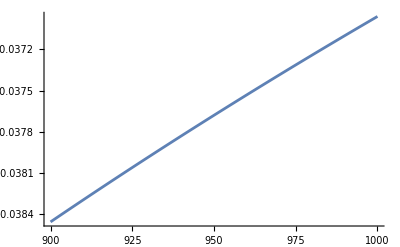

```mathematica
Plot[NIntegrate[i1[Δt,ρ],{Δt,1,2}],{ρ,900,1000}]
```

```mathematica
NIntegrate[(ρ^1 i1[Δt,ρ]/.ρ->10^6),{Δt,1,2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Δt near {Δt} = {1.00190336804519368658385192194515411756583489477634429931640625}. NIntegrate obtained -4.83759 and 0.000118017 for the integral and error estimates.

-4.83759